# PHY410: Homework 1, Problem 2

## part (a) (tests)

```mathematica
Random[]
```

0.429285

```mathematica
Random[Integer]
```

0

```mathematica
Table[Random[Integer], {10}]
```

{1,0,0,0,1,0,0,0,1,1}

Tossing n coins, finding number of heads, repeating whole trial N times, and displaying resulting histogram.
Below: n=10 coins; and N=200 trials.

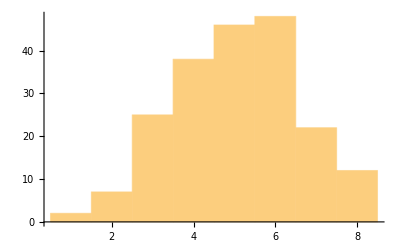

```mathematica
NumberOfHeads[n_] := Sum[Random[Integer], {n}]
ManyTrials[N_] := Table[NumberOfHeads[10], {N}]
Histogram[ManyTrials[200]]
```

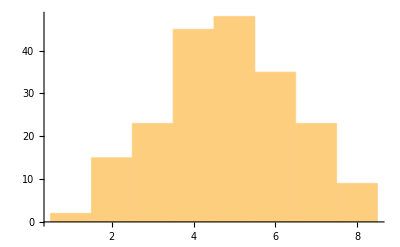

```mathematica
Histogram[Table[Sum[Random[Integer], {10}], {200}]]
```

## part (b)

Tossing 400 coins, finding number of heads, and repeating experiment 200 times.

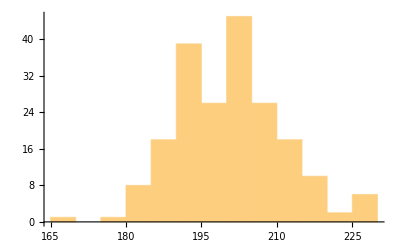

```mathematica
Histogram[Table[Sum[Random[Integer], {400}], {200}]]
```

Mathematica chose a bin width of 5, but I want the bni width to be 1, otherwise the Gaussian fit in part (d) won’t work. So I asked for 60 bins...

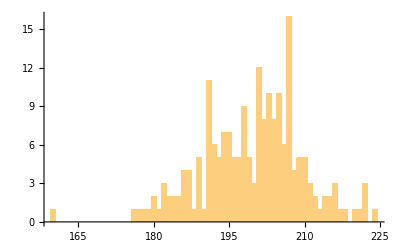

```mathematica
Histogram[Table[Sum[Random[Integer], {400}], {200}], 60]
```

## part (c)

Tossing 400 coins, finding number of heads, and repeating experiment 4000 times.

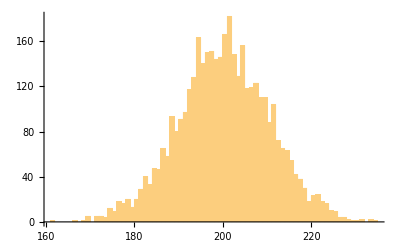

```mathematica
P1 = Histogram[Table[Sum[Random[Integer], {400}], {4000}], 80]
```

Tossing 100x more coins (40,000), but keeping the number of times experiment is repeated at 4000. Note no real change in shape of distribution... maybe... verify this...

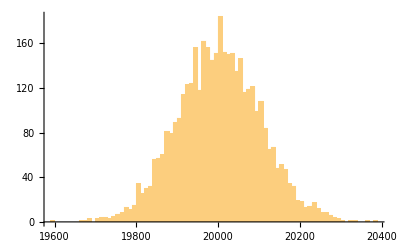

```mathematica
P3 = Histogram[Table[Sum[Random[Integer], {40000}], {4000}], 80]
```

Tossing same number of coins (400), but repeating the experiment 100x more times (400,000 times). Note that though the shape of the distribution appears sharper, but the exponential fit below only has to be multiplied by 100 to fit it perfectly (so technically steeper, but not particularly narrower/sharper). ...again I think.. verify this...

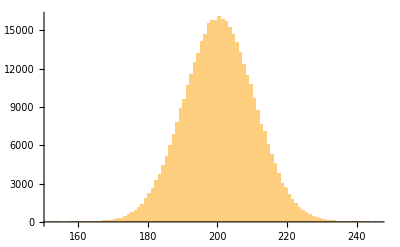

```mathematica
P4 = Histogram[Table[Sum[Random[Integer], {400}], {400000}], 80]
```

## part (d)

Graphing a Gaussian function to show how well it matches the above Histogram, P1. Normalized Gaussian multiplied by number of trials (4000) to match histogram, P1.
Note that function peaked at 200 (# heads out of 400), so exponential is centered via [n(#heads) - 200] and that this equals s, or the number of excess ‘spin’. So if there are 200 heads (& 200 tails), then there is no ‘excess spin’ and s=0. This point is where our binomial distribution would have the highest multiplicity, and therefore highest entropy.
Note also, that decreasing number of

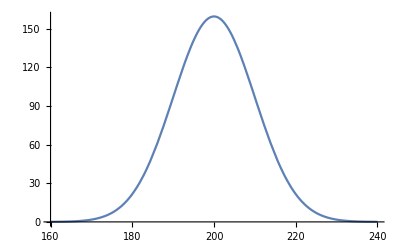

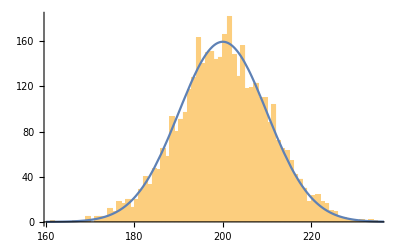

```mathematica
P2 = Plot[4000*Sqrt[2/(400*Pi)]*Exp[-2*(x-200)^2/400], {x, 160, 240}]
Show[P1, P2]
```